# CS164 5.2 PCW

## Lagrange Multiplier

Problem One:
First, we find the partial derivatives:

```mathematica
function[x_,y_]:=x^2+2y^2-4y
D[function[x,y],x]
D[function[x,y],y]
```

2 x

-4+4 y

Then we solve for the system of equations:

```mathematica
Solve[{2 x==L*2x},{x,L}]
```

{{L→1},{x→0}}

```mathematica
Solve[{-4+4 y==L*2y},{y}]
```

{{y→-2/(-2+L)}}

```mathematica
Solve[(-2/(-2+L))^2==9,{L}]
```

{{L→4/3},{L→8/3}}

The case where x = 0:

```mathematica
function[0,-2/(-2+4/3)]
```

6

```mathematica
function[0,-2/(-2+8/3)]
```

30

The case where L = 1:
The value of y would be (-2) if we plug in this value into the constraint function then the value of x would be (√5).
After inserting these values into the objective function, the output would be (5) which is considered to be the minimum under the given constraint.

We can then check the results on Mathematica built in function:

```mathematica
Minimize[x^2+2y^2-4y, x^2+y^2==9,{x,y}]
```

{5,{x→-√5,y→2}}

```mathematica
Maximize[x^2+2y^2-4y, x^2+y^2==9,{x,y}]
```

{30,{x→0,y→-3}}

Problem Two:

Cobb-Douglas function under constraints:

```mathematica
CobbDouglas[x_,y_]:=100x^(3/4)*y^(1/4)
D[CobbDouglas[x,y],x]
D[CobbDouglas[x,y],y]
```

(75 y^(1/4))/x^(1/4)

(25 x^(3/4))/y^(3/4)

```mathematica
constraint[x_,y_]:=200x+250y
D[constraint[x,y],x]
D[constraint[x,y],y]
```

200

250

```mathematica
Solve[D[CobbDouglas[x,y],x]==L*D[constraint[x,y],x],{x}]
```

{{x→(81 y)/(4096 L^4)}}

```mathematica
Solve[D[CobbDouglas[x,y],y]==L*D[constraint[x,y],y],{y}]
```

{{y→x^(3/4)/(10 10^(1/3) L (L/x^(3/4))^(1/3))}}

```mathematica
Solve[constraint[(81 y)/(4096 L^4),y]==50000,{y}]
```

{{y→(1024000 L^4)/(81+5120 L^4)}}

```mathematica
Solve[constraint[x,x^(3/4)/(10 10^(1/3) L (L/x^(3/4))^(1/3))]==50000,{x}∈Reals]
```

Solve[(5 5^(2/3) x^(3/4))/(2^(1/3) L (L/x^(3/4))^(1/3))+200 x==50000,x∈ℝ]

```mathematica
Show[Plot3D[CobbDouglas[x,y],{x,0,200},{y,0,200},PlotStyle-> Blue],Plot3D[200x+250y==50000,{x,0,200},{y,0,200},PlotStyle-> Red],PlotRange-> Automatic]
```

-Graphics3D-

The contour plot of the Cobb-Douglas function and the constraint:

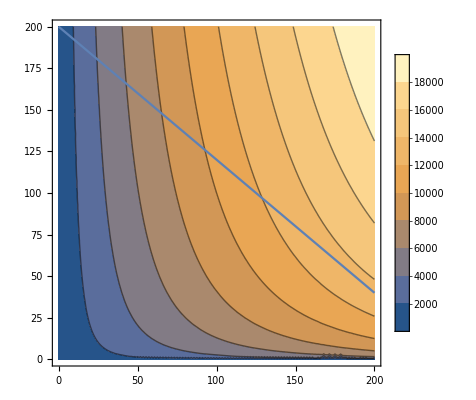

```mathematica
Show[ContourPlot[CobbDouglas[x,y],{x,0,200},{y,0,200},PlotLegends->Automatic],ContourPlot[200x+250y==50000,{x,0,200},{y,0,200}],PlotRange-> Automatic]
```

```mathematica
Maximize[{CobbDouglas[x,y],200x+250y==50000},{x,y}]
```

{-100 Root[-1318359375+4 #1^4&,1],{x→375/2,y→50}}

```mathematica
Evaluate[CobbDouglas[375/2,50]]
```

1250 √2 15^(3/4)